```mathematica
e1 = {1,0,0};e2 = {0,1,0};e3 = {0,0,1};
```

```mathematica
x1={0,-3.84139551244236*^-20};
x2={0.499820574375223,-9.13269976022856*^-05};
x3={1,-2.19181124420051*^-20};
x4={0.499820574375223,0.999908673002398};
x5={2.06878641964059*^-21,1};
x6={-0.500179425624777,0.999908673002398};
x7={0.249423966709635,0.499798241269122};

y1 = {1.93185165257814,-1.23277580121722*10^-20,5.88834139710597*10^-20};
y2 = {1.80771005351506, 0.00326008481105843,-0.483944003208976};
y3 = {1.67303260747562, 3.28507842606033*10^-19,-0.965925826289068};
y4 = {1.80771005351506, 1.00326008481106, -0.483944003208976};
y5 = {1.93185165257814, 1, -3.33863545509152*10^-19};
y6 = {1.80749483062506, 1.00326008481106, 0.484747225969420};
y7 = {1.87270853546523, 0.500741442747682, -0.248778026423960};

(*y1 = {1.73866648732032,-6.73982561740301*10^-19,-2.69197446073104*10^-18};
y2 = {1.80689659817071, 0.00973275326390280, -0.481252383149223};
y3 = {1.50572934672805, 1.65146736052503*10^-17,-0.869333243660161};
y4 = {1.80689659817071, 1.00973275326390, -0.481252383149223};
y5 = {1.73866648732032, 1, -2.50748594029268*10^-17};
y6 = {1.80544454760213,1.00973275326390,0.486671509646328};
y7 = {1.87001887048721, 0.504043009061202, -0.235668812408836};*)
```

```mathematica
t1x = x3 - x1;
t2x = x5 - x1;
g1x[{x01_,x02_}] = {x01,x02} + t1x;
g2x[{x01_,x02_}] = {x01,x02} + t2x;

pStar = 12; qStar = 0;
```

```mathematica
e = e2;
```

```mathematica
τ1 = 0;
```

```mathematica
Ident = {{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
Pe = Ident - Outer[Times,e,e];
```

```mathematica
θ1 = π/6;
```

```mathematica
τ2 = e.({0.5*0.7, 3*0.8, 0});
```

```mathematica
θ2 = 0;
```

```mathematica
pStar*θ1 + qStar*θ2 - 2*π
```

0

```mathematica
ReVec[θ_] = RotationMatrix[θ,e];
```

```mathematica
z = e3;
T1 = {0, 0, 0};
T2 = {0, 1, 0};
```

```mathematica
g1[{x01_,x02_,x03_}] = ReVec[θ1].({x01,x02,x03}) + T1;
```

```mathematica
g2[{x01_,x02_,x03_}] = ReVec[θ2].({x01,x02,x03}) + T2;
```

```mathematica
g2[y1]-y5
```

{0.,0.,3.92747×10^-19}

```mathematica
g1[y1]-y3
```

{-1.55431×10^-15,-3.40836×10^-19,-1.9984×10^-15}

```mathematica
g1x[x1]-x3
g2x[x1]-x6
```

{0,0.}

{0.500179,0.000091327}

```mathematica
IStep = 13; JStep = 3;
```

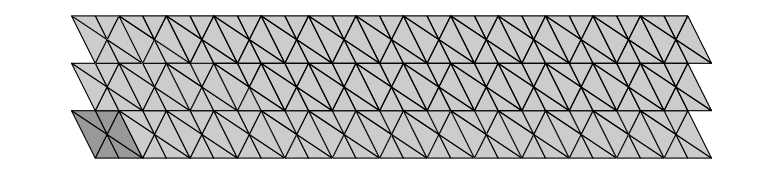

```mathematica
(* Final x *)
(*newOrange=RGBColor[0.95,0.55,0.33];*)
backgroundCellColor = GrayLevel[0.8];
unitCellColor = GrayLevel[0.6];
dPoly2D=Table[{
backgroundCellColor,  Polygon[{Nest[g1x,Nest[g2x,x1,j],i],Nest[g1x,Nest[g2x,x2,j],i],Nest[g1x,Nest[g2x,x7,j],i]}],backgroundCellColor, Polygon[{Nest[g1x,Nest[g2x,x2,j],i],Nest[g1x,Nest[g2x,x3,j],i],Nest[g1x,Nest[g2x,x7,j],i]}],backgroundCellColor, Polygon[{Nest[g1x,Nest[g2x,x3,j],i],Nest[g1x,Nest[g2x,x4,j],i],Nest[g1x,Nest[g2x,x7,j],i]}],backgroundCellColor, Polygon[{Nest[g1x,Nest[g2x,x4,j],i],Nest[g1x,Nest[g2x,x5,j],i],Nest[g1x,Nest[g2x,x7,j],i]}], backgroundCellColor, Polygon[{Nest[g1x,Nest[g2x,x5,j],i],Nest[g1x,Nest[g2x,x6,j],i],Nest[g1x,Nest[g2x,x7,j],i]}],
backgroundCellColor, Polygon[{Nest[g1x,Nest[g2x,x1,j],i],Nest[g1x,Nest[g2x,x6,j],i],Nest[g1x,Nest[g2x,x7,j],i]}]},{i,1,IStep},{j,1,JStep}];
dPoly2D[[1,1]] = {
unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x1,1],1],Nest[g1x,Nest[g2x,x2,1],1],Nest[g1x,Nest[g2x,x7,1],1]}],unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x2,1],1],Nest[g1x,Nest[g2x,x3,1],1],Nest[g1x,Nest[g2x,x7,1],1]}],unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x3,1],1],Nest[g1x,Nest[g2x,x4,1],1],Nest[g1x,Nest[g2x,x7,1],1]}],unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x4,1],1],Nest[g1x,Nest[g2x,x5,1],1],Nest[g1x,Nest[g2x,x7,1],1]}], unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x5,1],1],Nest[g1x,Nest[g2x,x6,1],1],Nest[g1x,Nest[g2x,x7,1],1]}],
unitCellColor, Polygon[{Nest[g1x,Nest[g2x,x1,1],1],Nest[g1x,Nest[g2x,x6,1],1],Nest[g1x,Nest[g2x,x7,1],1]}]};
Graphics[{EdgeForm[{Black, Thin}],dPoly2D}]
```

```mathematica
dPoly = Array[dP,{IStep,JStep}];
For[j=1,j<JStep+1,j++ ,For[i = 1,i< IStep+1,i++,dP[i,j]={Polygon[{Nest[g1,Nest[g2,y1,j],i],Nest[g1,Nest[g2,y2,j],i],Nest[g1,Nest[g2,y7,j],i]}],Polygon[{Nest[g1,Nest[g2,y2,j],i],Nest[g1,Nest[g2,y3,j],i],Nest[g1,Nest[g2,y7,j],i]}],
Polygon[{Nest[g1,Nest[g2,y3,j],i],Nest[g1,Nest[g2,y4,j],i],Nest[g1,Nest[g2,y7,j],i]}],
Polygon[{Nest[g1,Nest[g2,y4,j],i],Nest[g1,Nest[g2,y5,j],i],Nest[g1,Nest[g2,y7,j],i]}],
Polygon[{Nest[g1,Nest[g2,y5,j],i],Nest[g1,Nest[g2,y6,j],i],Nest[g1,Nest[g2,y7,j],i]}],
Polygon[{Nest[g1,Nest[g2,y1,j],i],Nest[g1,Nest[g2,y6,j],i],Nest[g1,Nest[g2,y7,j],i]}]}]]
```

```mathematica
Graphics3D[{EdgeForm[Opacity[.1]],dPoly},Boxed->False]
```

-Graphics3D-

```mathematica
fadedDP=dPoly/. p_Polygon:>{Opacity[0.2],p};
fadedDP[[1,2]]=dPoly[[1,2]];
Graphics3D[{EdgeForm[Opacity[0.25]],fadedDP},Boxed->False]
```

-Graphics3D-